```mathematica
(*num2lab2*)
path1 = NotebookDirectory[];
```

```mathematica
abserr1=Import[path1<>"abserr_3ex.txt","Table"];
```

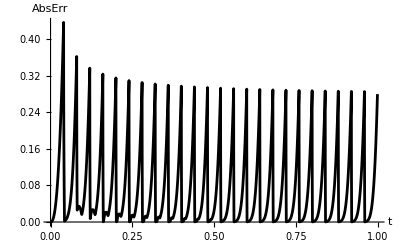

```mathematica
ListLinePlot[abserr1,AxesLabel->{Style[t,FontFamily->"Times",Black,Medium,Italic],Style[AbsErr,FontFamily->"Times",Black,Medium,Italic]},PlotStyle->{FontFamily->"Times",Black},LabelStyle->{Medium}]
```

```mathematica
Kux = 1;
L = 1;
P=-5;
C1=1;
B=0;
T0=-P/Kux x + B+C1 Cos[(π x)/L];
Ω=Rectangle[{0,0},{L,0.1}];
sol1 =u[x,t]/.DSolve[{D[u[x,t],t]==D[u[x,t],{x,2}],u[x,0]==T0,(D[u[x,t],x]/.x->0)==-P,(D[u[x,t],x]/.x->L)==-P},u[x,t],{x,t}∈Ω][[1]]
```

5 x+ⅇ^(-π^2 t) Cos[π x]

```mathematica
Plot3D[sol1,{x,t}∈Ω]
```

-Graphics3D-

```mathematica
Kux = 1/10;
L = 1;
C1=100;
T0=5;
TL=100;
ux0=T0+(TL-T0)/L x+C1 Sin[(π x)/L];
Ω=Rectangle[{0,0},{L,2}];
sol2 =u[x,t]/.DSolve[{D[u[x,t],t]==Kux*D[u[x,t],{x,2}],u[x,0]==ux0,u[0,t]==T0,u[L,t]==TL},u[x,t],{x,t}∈Ω][[1]]
```

5+95 x+100 ⅇ^(-(π^2 t)/10) Sin[π x]

```mathematica
Plot3D[sol2,{x,t}∈Ω]
```

-Graphics3D-

```mathematica
sol2/.{x->1,t->0}
```

100

```mathematica
shodh=Import[path1<>"lab2_shod_h.txt","Table"];
shodh2=Import[path1<>"lab2_shod_h2.txt","Table"];
shodh4=Import[path1<>"lab2_shod_h4.txt","Table"];
```

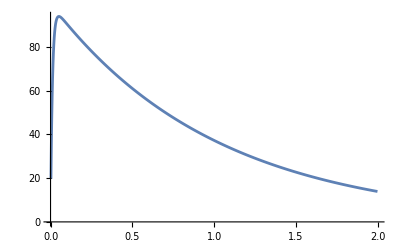

```mathematica
ListLinePlot[shodh]
```

```mathematica
points1=Import[path1<>"lab2_points.txt","Table"]
ListPointPlot3D[points1]
```

-Graphics3D-

```mathematica
points2=Import[path1<>"lab2_points_err.txt","Table"]
ListPointPlot3D[points2]
```

-Graphics3D-

```mathematica
points1[[49476]]
sol2/.{t->9.9,x->0.510204}
```

{9.9,0.510204,91.0905}

53.4751

```mathematica
h1=1/49*25//N
0.01*990//N
```

0.510204

9.9

```mathematica
(*i=25, k=990*)
```